# Projecto TAFC

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]
```

### Definição de variáveis

```mathematica
l[i_,t_]:=√((x[t]-xtoe[i])^2+(y[t]-ytoe[i])^2)
F[i_,t_]:=k(l0-l[i,t])
```

### Fase 1 - Suporte único

```mathematica
f1x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]
f1y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))

### Fase 2 -Duplo suporte

```mathematica
f2x=F[1,t]/m(x[t]-xtoe[1])/l[1,t]+F[2,t]/m(x[t]-xtoe[2])/l[2,t]
f2y=F[1,t]/m(y[t]-ytoe[1])/l[1,t]+F[2,t]/m(y[t]-ytoe[2])/l[2,t]-g
```

(k (x[t]-xtoe[1]) (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (x[t]-xtoe[2]) (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

-g+(k (l0-√((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2)) (y[t]-ytoe[1]))/(m √((x[t]-xtoe[1])^2+(y[t]-ytoe[1])^2))+(k (l0-√((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2)) (y[t]-ytoe[2]))/(m √((x[t]-xtoe[2])^2+(y[t]-ytoe[2])^2))

### mapa de poincare

```mathematica
If[ Length[poincaremap]==0,
poincaremap={{"Energia","Ang_TD","Pos_ini(y)","x0'","y1","y1'","x1","x1'","teta1","teta1'","y2","y2'","x2","x2'","teta2","teta2'"}};];
energiamin=800;
energiamax=840;
listaenergias=Subdivide[energiamin,energiamax,40];
params={k->14000,g->9.81,m->80,l0->1.0};
l0=l0/.params;
For[penergy=1,penergy≤Length[listaenergias],penergy++,
Print[penergy];
Energy=Part[listaenergias,penergy];
tetamin=π/2-π/5;
tetamax=π/2;
listateta=Subdivide[tetamin,tetamax,30];
For[pteta=1,pteta≤Length[listateta],pteta++,
If[Mod[pteta,IntegerPart[0.25Length[listateta]]]==0,Print[N[pteta/Length[listateta] 100]]];

ymin=l0 Sin [Part[listateta,pteta]];
ymax=l0;
listay=Subdivide [ymin,ymax,25];
(*parametros numéricos e condições iniciais*)
For[p=1,p<=Length[listay],p++,

f1nx=f1x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2nx=f2x/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f1ny=f1y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
f2ny=f2y/.{x[t]->xn[i],y[t]->yn[i]}/.params;
(*Posição Inicial do CoM no eixo x*)
xn[0]=0;
(*Inicialização do calcanhar*)
xtoe[1]=0;
ytoe[1]=0;

(*Ângulo de Touchdown, ângulo de ataque, é o ângulo ao qual chegada a posição l0 Sin [θcrit] troca-se de single para double support*)
θcrit=Part[listateta,pteta];
(*começamos com single support*)
cases=1;
(*Parametros numéricos*)
Nmax=1500;
Δt =0.001;

(*Parametros a mudar*)

(*Altura inicial da perna*)
yn[0]=Part[listay,p];

(*Velocidade, obtida da energia*)
v=√(2/m(Energy-m g yn[0] - k/2(l0-yn[0])^2))/.params;
(*ângulo da velocidade*)
α0=0;
xn'[0]=v Cos[α0];
yn'[0]=v Sin[α0];
For[i=0;step=0;L1={0};record=1;stepMAX=2,i<=Nmax,i++,

(*Suporte Único*)
(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==1,
K1vx=f1nx;
K2vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K1vx,yn[i]->yn[i]+0.5Δt K1vx};
K3vx=f1nx/.{xn[i]->xn[i]+0.5 Δt K2vx,yn[i]->yn[i]+0.5Δt K2vx};
K4vx=f1nx/.{xn[i]->xn[i]+ Δt K3vx,yn[i]->yn[i]+Δt K3vx};
xn'[i+1]=xn'[i]+Δt/6(K1vx+2K2vx+2K3vx+K4vx);

(*Vy*)
K1vy=f1ny;
K2vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K1vy,yn[i]->yn[i]+0.5Δt K1vy};
K3vy=f1ny/.{xn[i]->xn[i]+0.5 Δt K2vy,yn[i]->yn[i]+0.5Δt K2vy};
K4vy=f1ny/.{xn[i]->xn[i]+ Δt K3vy,yn[i]->yn[i]+Δt K3vy};
yn'[i+1]=yn'[i]+Δt/6(K1vy+2K2vy+2K3vy+K4vy);


(*Runge kutta para as posições*)
(*X*)
K1x=xn'[i];
K2x=xn'[i]+0.5Δt K1x;
K3x=xn'[i]+0.5 Δt K2x;
K4x=xn'[i]+Δt K3x;

xn[i+1]=xn[i]+Δt/6(K1x+2K2x+2K3x+K4x);
(*Y*)
K1y=yn'[i];
K2y=yn'[i]+0.5Δt K1y;
K3y=yn'[i]+0.5 Δt K2y;
K4y=yn'[i]+Δt K3y;

yn[i+1]=yn[i]+Δt/6(K1y+2K2y+2K3y+K4y)];
(*Suporte Duplo*)

(* Runge kutta para as velocidades*)
(*Vx*)
If[cases==2,
G1vx=f2nx;
G2vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G1vx,yn[i]->yn[i]+0.5Δt G1vx};
G3vx=f2nx/.{xn[i]->xn[i]+0.5 Δt G2vx,yn[i]->yn[i]+0.5Δt G2vx};
G4vx=f2nx/.{xn[i]->xn[i]+ Δt G3vx,yn[i]->yn[i]+Δt G3vx};
xn'[i+1]=xn'[i]+Δt/6(G1vx+2G2vx+2G3vx+G4vx);

(*Vy*)
G1vy=f2ny;
G2vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G1vy,yn[i]->yn[i]+0.5Δt G1vy};
G3vy=f2ny/.{xn[i]->xn[i]+0.5 Δt G2vy,yn[i]->yn[i]+0.5Δt G2vy};
G4vy=f2ny/.{xn[i]->xn[i]+ Δt G3vy,yn[i]->yn[i]+Δt G3vy};
yn'[i+1]=yn'[i]+Δt/6(G1vy+2G2vy+2G3vy+G4vy);

(*Runge kutta para as posições*)
(*X*)
G1x=xn'[i];
G2x=xn'[i]+0.5Δt G1x;
G3x=xn'[i]+0.5 Δt G2x;
G4x=xn'[i]+Δt G3x;

xn[i+1]=xn[i]+Δt/6(G1x+2G2x+2G3x+G4x);
(*Y*)
G1y=yn'[i];
G2y=yn'[i]+0.5Δt G1y;
G3y=yn'[i]+0.5 Δt G2y;
G4y=yn'[i]+Δt G3y;

yn[i+1]=yn[i]+Δt/6(G1y+2G2y+2G3y+G4y)];

(*transição single support para double support*)
If[cases==1 &&yn'[i]<0&& yn[i]<=l0 Sin[θcrit]&&yn[i-1]>l0 Sin[θcrit]&&i>10 && caso[i-1]≠2,

cases=2;
xtoe[2]=xn[i]+l0 Cos[θcrit];
ytoe[2]=0];

(*transição de double support para single support*)
If[cases==2 &&  √((xn[i]-xtoe[1])^2+(yn[i]-ytoe[1])^2)≥l0 (*||√((xn[i]-xtoe[2])^2+(yn[i]-ytoe[2])^2)≥l0*), 
xtoe[1]=xtoe[2];
ytoe[1]=ytoe[2];
cases=1];

caso[i]=cases;
xtoe1i[i]=xtoe[1];
xtoe2i[i]=xtoe[2];
If[(xn[i]-xtoe1i[i])>0&&(xn[i-1]-xtoe1i[i-1])<0&&caso[i]==1 &&caso[i-1]!=2 ,
L1=Join[L1,{i}];
step=step+1];
If[step==stepMAX ,
istepmax=i;
Break[]];
If[yn[i]<0||yn[i]>l0||xn'[i]<0,
record=0;
Break[]]
];

interx=Interpolation[Table[xn[i ],{i,0,Part[L1,Length[L1]]}]];
intery=Interpolation[Table[yn[i ],{i,0,Part[L1,Length[L1]]}]];
intervx=Interpolation[Table[xn'[i ],{i,0,Part[L1,Length[L1]]}]];
intervy=Interpolation[Table[yn'[i ],{i,0,Part[L1,Length[L1]]}]];
roots=Table[r/.FindRoot[interx[r]==xtoe1i[Part[L1,n]],{r,3}],{n,2,Length[L1]}];
If[Length[roots]≠2,record=0];

If[record==1,

poincaremap=Join[poincaremap,{{N[Energy/.params],N[θcrit],yn[0],N[interx'[0]],N[intery[Part[roots,1]]],N[intery'[Part[roots,1]]],N[interx[Part[roots,1]]],N[interx'[Part[roots,1]]],N[ArcTan[intervy[Part[roots,1]]/intervx[Part[roots,1]]]],N[(intervy'[Part[roots,1]]intervx[Part[roots,1]]-intervy[Part[roots,1]]intervx'[Part[roots,1]])/intervx[Part[roots,1]]^2 ArcTan'[intervy[Part[roots,1]]/intervx[Part[roots,1]]]],N[intery[Part[roots,2]]],N[intery'[Part[roots,2]]],N[interx[Part[roots,2]]],N[interx'[Part[roots,2]]],N[ArcTan[intervy[Part[roots,2]]/intervx[Part[roots,2]]]],N[(intervy'[Part[roots,2]]intervx[Part[roots,2]]-intervy[Part[roots,2]]intervx'[Part[roots,2]])/intervx[Part[roots,2]]^2 ArcTan'[intervy[Part[roots,2]]/intervx[Part[roots,2]]]]}}]];
Clear[i,xtoe,ytoe];
]]]

SetDirectory["/home/nteixeira/S1_2018_2019/PMEFT/TAFC/fixed_points"]
Export["Allfixedpointsv3.dat",poincaremap,"Table"]
```

1

Less::nord: Invalid comparison with 0.+1.50198 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+0.00150273 ⅈ attempted.

Less::nord: Invalid comparison with 0.+1.50198 ⅈ attempted.

Greater::nord: Invalid comparison with 0.+0.00300547 ⅈ attempted.

Less::nord: Invalid comparison with 0.+0.00150273 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 0.+0.00450826 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

22.5806

InterpolatingFunction::dmval: Input value {1303.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1332.31} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1258.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

45.1613

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

67.7419

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

90.3226

2

22.5806

45.1613

67.7419

90.3226

3

22.5806

45.1613

67.7419

90.3226

4

22.5806

45.1613

67.7419

90.3226

5

22.5806

45.1613

67.7419

90.3226

6

22.5806

45.1613

67.7419

90.3226

7

22.5806

45.1613

67.7419

90.3226

8

22.5806

45.1613

67.7419

90.3226

9

22.5806

45.1613

67.7419

90.3226

10

22.5806

45.1613

67.7419

90.3226

11

22.5806

45.1613

67.7419

90.3226

12

22.5806

45.1613

67.7419

90.3226

13

22.5806

45.1613

67.7419

90.3226

14

22.5806

45.1613

67.7419

90.3226

15

22.5806

45.1613

67.7419

90.3226

16

22.5806

45.1613

67.7419

90.3226

17

22.5806

45.1613

67.7419

90.3226

18

22.5806

45.1613

67.7419

90.3226

19

22.5806

45.1613

67.7419

90.3226

20

22.5806

45.1613

67.7419

90.3226

21

22.5806

45.1613

67.7419

90.3226

22

22.5806

45.1613

67.7419

90.3226

23

22.5806

45.1613

67.7419

90.3226

24

22.5806

45.1613

67.7419

90.3226

25

22.5806

45.1613

67.7419

90.3226

26

22.5806

45.1613

67.7419

90.3226

27

22.5806

45.1613

67.7419

90.3226

28

22.5806

45.1613

67.7419

90.3226

29

22.5806

45.1613

67.7419

90.3226

30

22.5806

45.1613

67.7419

90.3226

31

22.5806

45.1613

67.7419

90.3226

32

22.5806

45.1613

67.7419

90.3226

33

22.5806

45.1613

67.7419

90.3226

34

22.5806

45.1613

67.7419

90.3226

35

22.5806

45.1613

67.7419

90.3226

36

22.5806

45.1613

67.7419

90.3226

37

22.5806

45.1613

67.7419

90.3226

38

22.5806

45.1613

67.7419

90.3226

39

22.5806

45.1613

67.7419

90.3226

40

22.5806

45.1613

67.7419

90.3226

41

22.5806

45.1613

67.7419

90.3226

/home/nteixeira/Desktop/S1_2018_2019/PMEFT/TAFC/fixed_points

Allfixedpointsv3.dat

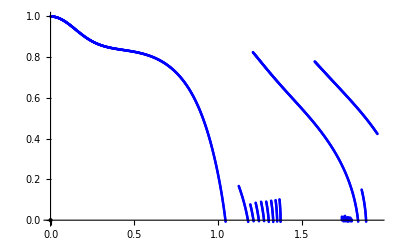

```mathematica
Show[ListPlot[Table[{xn[i],yn[i]},{i,0,Nmax}],PlotStyle->Blue],Graphics[Point[{xtoe1i[400],0}]],(*ListPlot[Table[{i,caso[i]},{i,0,Nmax}],PlotStyle->Red],*)PlotRange->All]
```

```mathematica
Manipulate[Show[Evaluate[If[caso[j]==2, Graphics[Line[{{xtoe2i[j],0},{xn[j],yn[j]}}]]]]/.Null->Sequence[],Graphics[Line[{{xtoe1i[j],0},{xn[j],yn[j]}}]],ListPlot[Table[{xn[i],yn[i]},{i,0,j}]],PlotRange->All(*{{0, Max[Table[{xn[i]},{i,0,Nmax1}]]},{0,1.0}}*)],{j,0,Nmax,1}]
istepmax
```

605

```mathematica
Information[istepmax]
```

Global`istepmax

istepmax=605

```mathematica
step
```

0

```mathematica
roots
```

{}

```mathematica
L1
```

{0}

```mathematica
t1={{2,3,19,29}}
```

{{2,3,19,29}}

```mathematica
Energy
```

840

```mathematica
listateta
```

{(3 π)/10,(23 π)/75,(47 π)/150,(8 π)/25,(49 π)/150,π/3,(17 π)/50,(26 π)/75,(53 π)/150,(9 π)/25,(11 π)/30,(28 π)/75,(19 π)/50,(29 π)/75,(59 π)/150,(2 π)/5,(61 π)/150,(31 π)/75,(21 π)/50,(32 π)/75,(13 π)/30,(11 π)/25,(67 π)/150,(34 π)/75,(23 π)/50,(7 π)/15,(71 π)/150,(12 π)/25,(73 π)/150,(37 π)/75,π/2}

```mathematica
Energy
```

840